Copyright ©, 2015, Erdong Guo and Shu Lin
Author: Erdong Guo and Shu Lin
E-mail: guoerdong@itp.ac.cn, linshu8@mail.sysu.edu.cn
Affliation: Institute of Theoretical Physics, Chinese Academy of Scineces, School of Physics and Astronomy, Sun-Yat Sen University
Description: Calculation tools for AdS/QCD. In this file, we provide an idea to explore the phase transition points of a themal quantum field theory by analyzing its dual theory of gravity using numerical technique.

```mathematica
H=1+1/#^4&;f=1-1/#^4&;
gtt=-r0^2/2 #^2 f[#]^2/H[#]&;
gxx=r0^2/2 #^2 H[#]&;
gphiphi=chi[#]^2&;
grhorho=1/#^2&;
L=Simplify[Sqrt[-gtt[rho] gxx[rho](gxx[rho]^2+B^2)(grhorho[rho]+chi'[rho]^2/(1-chi[rho]^2))(1-chi[rho]^2)^3]/.{r0-> 1},Assumptions->rho>1&&chi[rho]<1&&chi[rho]>0];
eom=3 (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho]^3-(-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho] (3+4 rho^2 chi'[rho]^2)+rho (-(3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]-4 rho^2 (1+rho^4) (1+2 B^2 rho^4+rho^8) chi'[rho]^3-rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho])+rho chi[rho]^2 ((3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]+rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho]);
FreeEnergyB[Chi0_,nB_,eps_,uv_]:=
Module[{sol,data,rep},
sol=NDSolve[{eom==0,chi[1+eps]==Chi0+eps^2/2 chi2+eps^3/6 chi3,chi'[1+eps]==eps chi2+eps^2/2 chi3}/.{chi2-> -3/2 Chi0,chi3-> 9/2 Chi0,B-> nB},chi,{rho,1+eps,uv},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25];data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];{rep=FindFit[data,m+c/rho^2,{m,c},rho],FE=NIntegrate[L/.sol[[1]]/.rep/.{B->nB},{rho,1+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-m^2)^2-4 m c)/.rep)+B^2/2 Log[uv]/.{B->nB})}]
chimi=chi0;
pchimi=-((2 a^2 (-1+a^4) (1+a^8+a^4 (2+4 B^2)) chi0+(a^4 (-9+13 chi0^2+a^24 (-15+19 chi0^2)-16 a^12 (3-2 chi0^2-2 B^2 (-3+chi0^2)+2 B^4 (3+chi0^2))+a^8 (-33+29 chi0^2+84 B^2 (-1+chi0^2)+8 B^4 (-3+11 chi0^2))+a^16 (-39+35 chi0^2+108 B^2 (-1+chi0^2)+8 B^4 (-9+17 chi0^2))+2 a^4 (-9+13 chi0^2+B^2 (-15+31 chi0^2))+a^20 (-30+38 chi0^2+B^2 (-66+98 chi0^2))))/(-54 a^6 chi0-162 a^10 chi0-198 a^14 chi0-162 a^18 chi0-54 a^22 chi0+126 a^26 chi0+198 a^30 chi0+162 a^34 chi0+108 a^38 chi0+36 a^42 chi0-450 a^10 B^2 chi0-846 a^14 B^2 chi0-666 a^18 B^2 chi0-198 a^22 B^2 chi0+522 a^26 B^2 chi0+774 a^30 B^2 chi0+594 a^34 B^2 chi0+270 a^38 B^2 chi0-1188 a^14 B^4 chi0-1260 a^18 B^4 chi0-72 a^22 B^4 chi0+648 a^26 B^4 chi0+1260 a^30 B^4 chi0+612 a^34 B^4 chi0-1008 a^18 B^6 chi0-432 a^22 B^6 chi0+1008 a^26 B^6 chi0+432 a^30 B^6 chi0+46 a^6 chi0^3+138 a^10 chi0^3+198 a^14 chi0^3+226 a^18 chi0^3+102 a^22 chi0^3-174 a^26 chi0^3-262 a^30 chi0^3-162 a^34 chi0^3-84 a^38 chi0^3-28 a^42 chi0^3+354 a^10 B^2 chi0^3+750 a^14 B^2 chi0^3+954 a^18 B^2 chi0^3+486 a^22 B^2 chi0^3-810 a^26 B^2 chi0^3-1062 a^30 B^2 chi0^3-498 a^34 B^2 chi0^3-174 a^38 B^2 chi0^3+804 a^14 B^4 chi0^3+1644 a^18 B^4 chi0^3+840 a^22 B^4 chi0^3-1416 a^26 B^4 chi0^3-1644 a^30 B^4 chi0^3-228 a^34 B^4 chi0^3+496 a^18 B^6 chi0^3+1968 a^22 B^6 chi0^3-2544 a^26 B^6 chi0^3+80 a^30 B^6 chi0^3+√(a^12 ((-4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2-3 (1+a^4) (1+a^8+2 a^4 B^2) (3+5 a^12+a^4 (3+4 B^2)+a^8 (5+12 B^2)) (-1+chi0^2))^3+4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2 (-27+23 chi0^2+2 a^24 (-9+7 chi0^2)-a^16 (63-67 chi0^2-162 B^2 (-1+chi0^2)+2 B^4 (27+5 chi0^2))+a^20 (4 (-9+7 chi0^2)+B^2 (-63+31 chi0^2))+2 a^8 (-36+38 chi0^2+99 B^2 (-1+chi0^2)+B^4 (-63+31 chi0^2))+2 a^12 (-45+53 chi0^2+2 B^2 (-45+61 chi0^2)+2 B^4 (-45+77 chi0^2))+a^4 (-54+46 chi0^2+B^2 (-117+85 chi0^2)))^2)))^(1/3)+(-54 a^6 chi0-162 a^10 chi0-198 a^14 chi0-162 a^18 chi0-54 a^22 chi0+126 a^26 chi0+198 a^30 chi0+162 a^34 chi0+108 a^38 chi0+36 a^42 chi0-450 a^10 B^2 chi0-846 a^14 B^2 chi0-666 a^18 B^2 chi0-198 a^22 B^2 chi0+522 a^26 B^2 chi0+774 a^30 B^2 chi0+594 a^34 B^2 chi0+270 a^38 B^2 chi0-1188 a^14 B^4 chi0-1260 a^18 B^4 chi0-72 a^22 B^4 chi0+648 a^26 B^4 chi0+1260 a^30 B^4 chi0+612 a^34 B^4 chi0-1008 a^18 B^6 chi0-432 a^22 B^6 chi0+1008 a^26 B^6 chi0+432 a^30 B^6 chi0+46 a^6 chi0^3+138 a^10 chi0^3+198 a^14 chi0^3+226 a^18 chi0^3+102 a^22 chi0^3-174 a^26 chi0^3-262 a^30 chi0^3-162 a^34 chi0^3-84 a^38 chi0^3-28 a^42 chi0^3+354 a^10 B^2 chi0^3+750 a^14 B^2 chi0^3+954 a^18 B^2 chi0^3+486 a^22 B^2 chi0^3-810 a^26 B^2 chi0^3-1062 a^30 B^2 chi0^3-498 a^34 B^2 chi0^3-174 a^38 B^2 chi0^3+804 a^14 B^4 chi0^3+1644 a^18 B^4 chi0^3+840 a^22 B^4 chi0^3-1416 a^26 B^4 chi0^3-1644 a^30 B^4 chi0^3-228 a^34 B^4 chi0^3+496 a^18 B^6 chi0^3+1968 a^22 B^6 chi0^3-2544 a^26 B^6 chi0^3+80 a^30 B^6 chi0^3+√(a^12 ((-4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2-3 (1+a^4) (1+a^8+2 a^4 B^2) (3+5 a^12+a^4 (3+4 B^2)+a^8 (5+12 B^2)) (-1+chi0^2))^3+4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2 (-27+23 chi0^2+2 a^24 (-9+7 chi0^2)-a^16 (63-67 chi0^2-162 B^2 (-1+chi0^2)+2 B^4 (27+5 chi0^2))+a^20 (4 (-9+7 chi0^2)+B^2 (-63+31 chi0^2))+2 a^8 (-36+38 chi0^2+99 B^2 (-1+chi0^2)+B^4 (-63+31 chi0^2))+2 a^12 (-45+53 chi0^2+2 B^2 (-45+61 chi0^2)+2 B^4 (-45+77 chi0^2))+a^4 (-54+46 chi0^2+B^2 (-117+85 chi0^2)))^2)))^(1/3))/(6 a^3 (1+a^4) (1+a^8+2 a^4 B^2)));
FreeEnergyM[a0_,nB_,eps_,uv_]:=
Module[{sol,data,rep},
sol=NDSolve[{eom==0,chi[a0]==chi0,chi'[a0]==pchimi}/.{a->a0,chi0-> 1-eps,B-> nB},chi,{rho,a0,uv},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25];data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];{rep=FindFit[data,m+c/rho^2,{m,c},rho],FE=NIntegrate[L/.sol[[1]]/.rep/.{B->nB},{rho,a0,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-m^2)^2-4 m c)/.rep)+B^2/2 Log[uv]/.{B->nB})}]
```

```mathematica
FEM[initb_,nb_,nm_,stplb_,stplm_,nB_]:=
Module[{datab,datam,datamb},
datab=Table[{1/(FreeEnergyB[initb+i stplb,nB,1/100 ,100][[-2]][[1]][[-1]]),FreeEnergyB[initb+i stplb,nB,1/100,100][[-1]]},{i,nb}];datam=Table[{1/(FreeEnergyM[1+i stplm,nB,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i stplm,nB,1/100,100][[-1]]},{i,nm}];
datamb=Table[{1/(FreeEnergyB[initb+i stplb,nB,1/100 ,100][[-2]][[1]][[-1]])-1/(FreeEnergyM[1+i stplm,nB,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[initb+i stplb,nB,1/100,100][[-1]]-FreeEnergyM[1+i stplm,nB,1/100,100][[-1]]},{i, nb}];
ListLinePlot[{datab,datam},PlotStyle->{Red,{Blue,Dashed}},AxesLabel->{Style["1/m",FontSize->18],Style["F",FontSize->18]},AxesStyle->12,PlotLabel->Style["B=8",FontSize->12]]]
```

```mathematica
FEM[9/10,60,60,1/601,1/300,0]
```

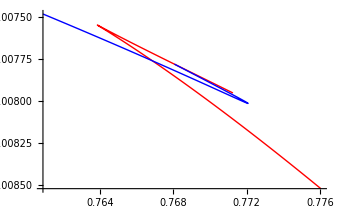
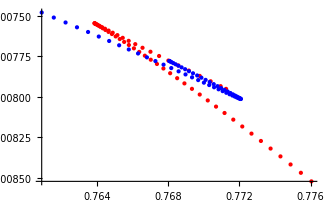
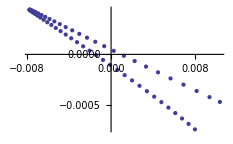

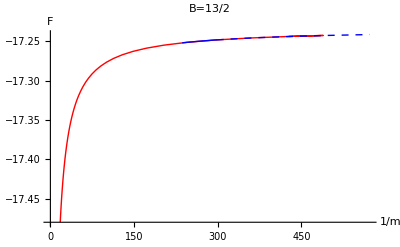

```mathematica
FEM[9/10,50,30,1/501,1/300,13/2]
```

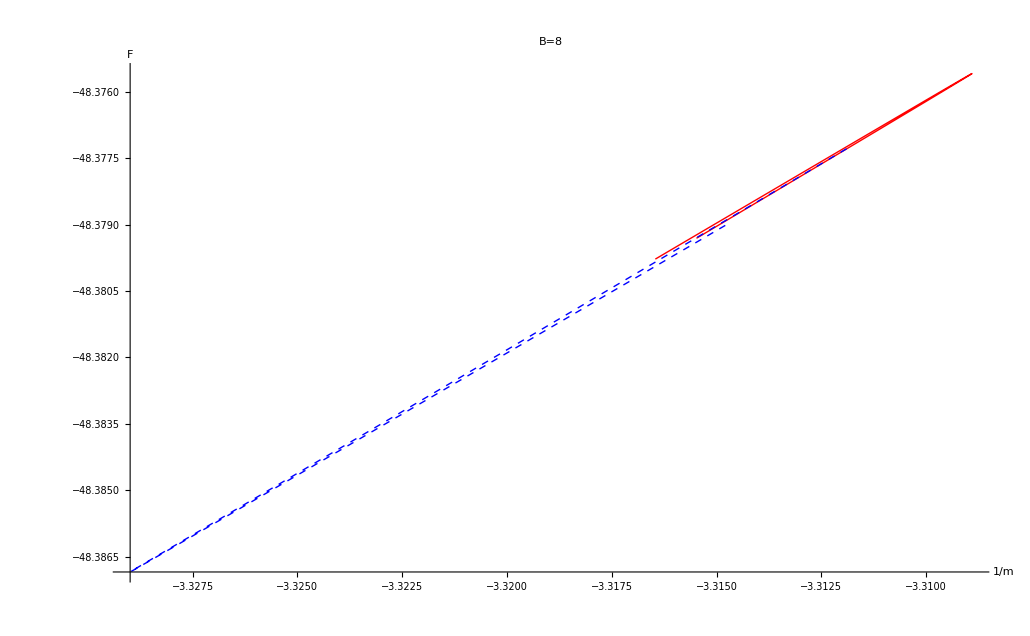

```mathematica
FEM[19/20+1/40+1/80,50,30,1/4001,1/300,10]
```

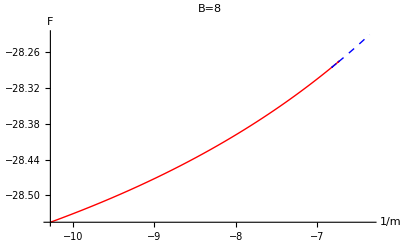

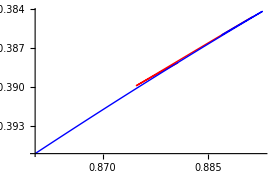
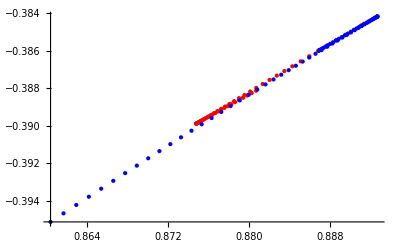
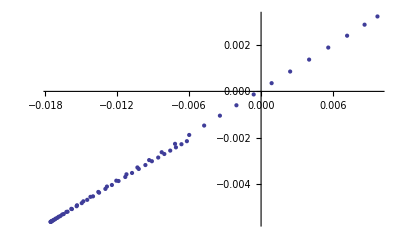

```mathematica
FEM[9/10,60,80,1/601,1/300,1]
```

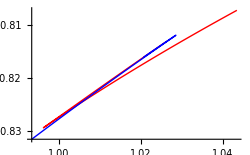
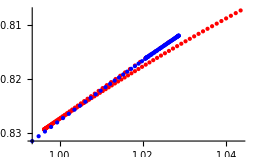
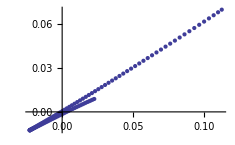

```mathematica
FEM[8/10,120,80,1/601,1/300,3/2]
```

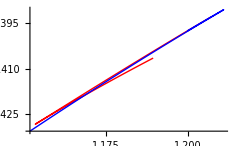
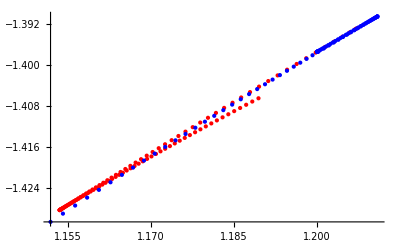
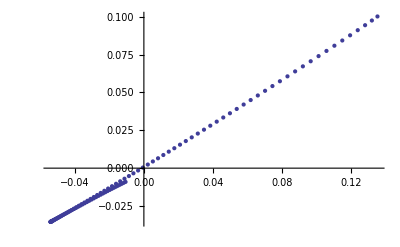

```mathematica
FEM[8/10,120,90,1/601,1/300,2]
```

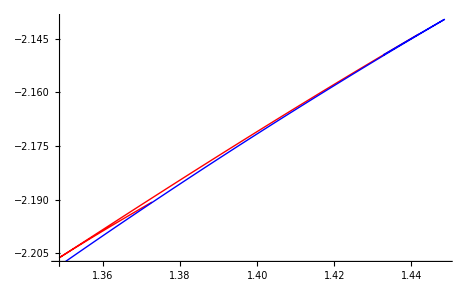
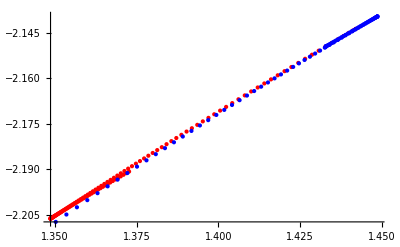
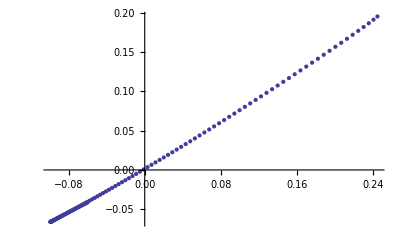

```mathematica
FEM[8/10,140,100,1/701,1/300,5/2]
```

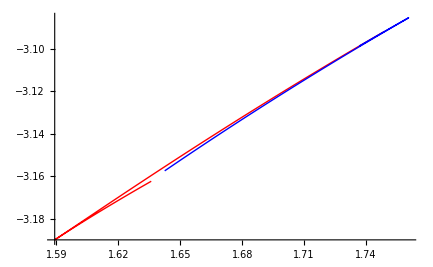
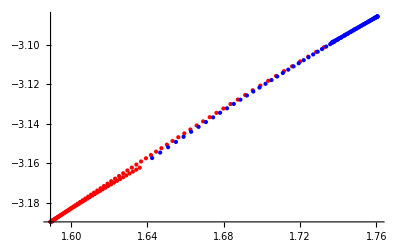
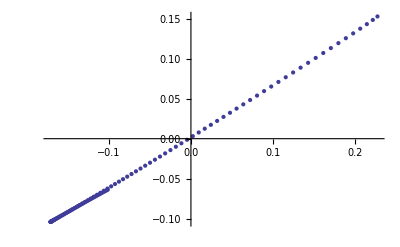

```mathematica
FEM[3/4,125,100,1/501,1/300,3]
```

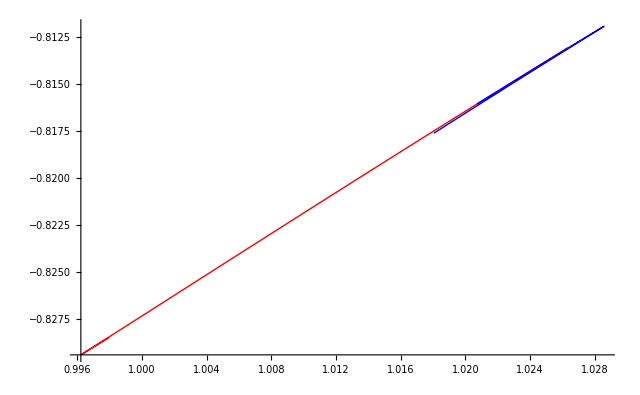
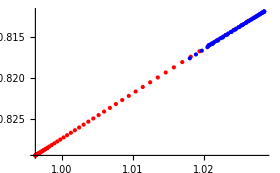
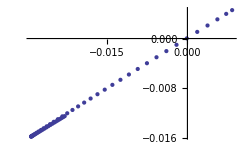
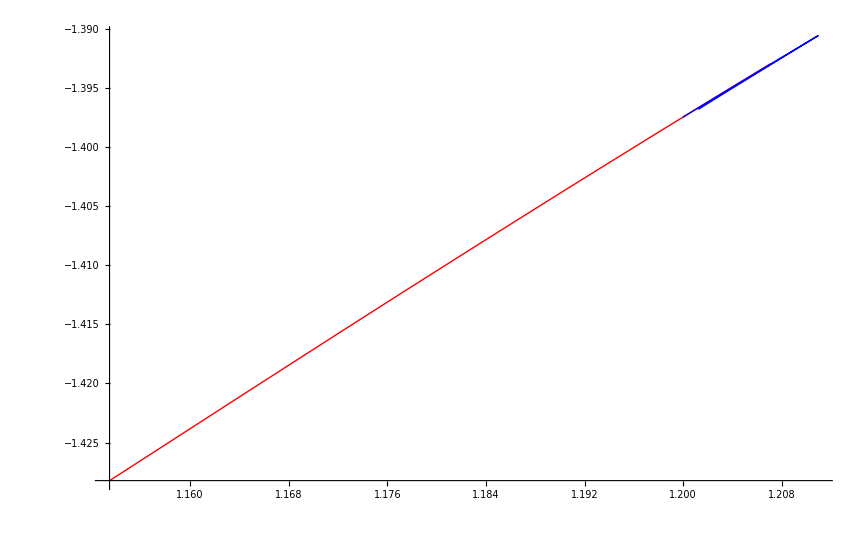
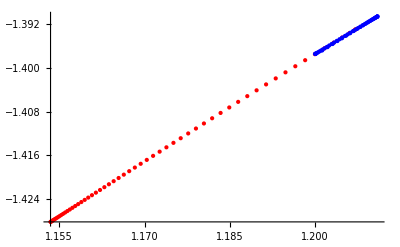
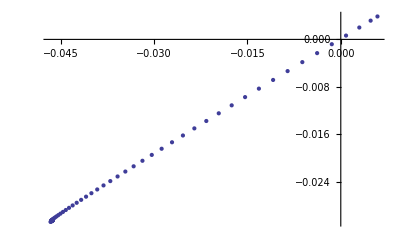
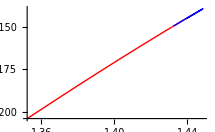
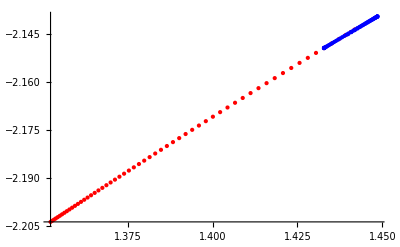

```mathematica
Table[{FEM[9/10,60,60,1/601,1/300,i/2]},{i,3,12}]
```